```mathematica
ClearAll;
```

```mathematica
TensVec[var_List,numvar_,numnos_,pred_List,suc_List,funcoes_List,direction_List]:=
Module[{v=Table[0,{numnos}],vd=Table[0,{numnos}],w,Td, dimpred=Flatten[Map[Dimensions,pred]], tempmap, tempvars,vadj =Table[0,{numnos}],
gradphii, hessphii, tensorphii,i,j,k,p,tempval,aux,a,b,c,d},
(* Inicializações *)
aux={a,b,c,d};
w = Table[0,{numnos},{numnos}] ;
Td =  Table[0,{numnos},{numnos}] ;
v[[Range[1,numvar]]]=var;
vd[[Range[1,numvar]]]=direction;
vadj[[numnos]] = 1;
For[i=numvar+1, i≤ numnos, i++,
v[[i]]=funcoes[[i-numvar]][v[[pred[[i]]]]];
(* Gradiente de phi_i*)
gradphii=D[funcoes[[i-numvar]][aux[[Range[1,dimpred[[i]]]]]],{aux[[Range[1,dimpred[[i]]]]]}]/.MapThread[Rule,{aux[[Range[1,dimpred[[i]]]]],v[[pred[[i]]]]}];
vd[[i]]=gradphii.vd[[pred[[i]]]];
(* vd[i] = sum_{j \in P(i)} vd[j] D_j phi_i *)
];
(*Reverse Sweep*)
For[i=numnos,i≥numvar+1,i--,
(* Cálculo de derivadas necessárias *)
(* Gradiente de phi_i*)
gradphii=D[funcoes[[i-numvar]][aux[[Range[1,dimpred[[i]]]]]],{aux[[Range[1,dimpred[[i]]]]]}]/.MapThread[Rule,{aux[[Range[1,dimpred[[i]]]]],v[[pred[[i]]]]}];
(* Hessiana de phi_i*)
hessphii=D[funcoes[[i-numvar]][aux[[Range[1,dimpred[[i]]]]]],{aux[[Range[1,dimpred[[i]]]]],2}]/.MapThread[Rule,{aux[[Range[1,dimpred[[i]]]]],v[[pred[[i]]]]}];
(* Tensor de phi_i*)
tensorphii=D[funcoes[[i-numvar]][aux[[Range[1,dimpred[[i]]]]]],{aux[[Range[1,dimpred[[i]]]]],3}]/.MapThread[Rule,{aux[[Range[1,dimpred[[i]]]]],v[[pred[[i]]]]}];
(************* Tensor Vector Iteration *****************)
(*Pushing*)
(*for Tdii not zero*)
For[j=1,j≤ dimpred[[i]],j++,
For[k=j,k≤dimpred[[i]],k++,
If[pred[[i,k]] > pred[[i,j]],
Td[[pred[[i,k]],pred[[i,j]]]]+=gradphii[[j]]*gradphii[[k]]*Td[[i,i]];(*Else*),
Td[[pred[[i,j]],pred[[i,k]]]]+=gradphii[[j]]*gradphii[[k]]*Td[[i,i]];
];
];
];
For[p=i-1,p≥1,p--,
For[j=1,j≤dimpred[[i]],j++,
If[pred[[i,j]]==p,
Td[[p,p]]+=2*gradphii[[j]]*Td[[i,p]];(*Else*),
If[pred[[i,j]] > p,
Td[[pred[[i,j]],p]]+=gradphii[[j]]*Td[[i,p]];(*Else*),
Td[[p,pred[[i,j]]]]+=gradphii[[j]]*Td[[i,p]];
];
];
];
];
(*2D connecting*)
(*wii not zero*)
For[p=1,p≤ dimpred[[i]],p++,
 For[j=1,j≤ dimpred[[i]],j++,
For[k=j,k≤dimpred[[i]],k++,(*in this version, this loop doesn't sum up everything*)
tempval=vd[[pred[[i,p]]]]*w[[i,i]]*(  gradphii[[j]]*hessphii[[k,p]]+gradphii[[k]]*hessphii[[j,p]]+gradphii[[p]]*hessphii[[j,k]]);
If[pred[[i,k]] > pred[[i,j]],
 Td[[pred[[i,k]],pred[[i,j]]]]+=tempval;(*Else*),
Td[[pred[[i,j]],pred[[i,k]]]]+=tempval;
];
];
];
];
(*wik not zero*)
For[k=i-1,k≥1,k--, 
For[p=1,p≤ dimpred[[i]],p++,
 For[j=1,j≤ dimpred[[i]],j++,
If[pred[[i,j]]==k,
Td[[k,k]]+= 2*vd[[pred[[i,p]]]]*w[[i,k]]*hessphii[[j,p]];
];
If[pred[[i,j]] >  k,
Td[[pred[[i,j]],k]]+=vd[[pred[[i,p]]]]*w[[i,k]]*hessphii[[j,p]];];
If[pred[[i,j]] <  k,
Td[[k,pred[[i,j]]]]+=vd[[pred[[i,p]]]]*w[[i,k]]*hessphii[[j,p]];];
If[pred[[i,j]] >= pred[[i,p]],
Td[[pred[[i,j]],pred[[i,p]]]]+=vd[[k]]*w[[i,k]]*hessphii[[j,p]];];
];
];
];
(*3D creating*)
For[p=1,p≤ dimpred[[i]],p++,
 For[j=1,j≤ dimpred[[i]],j++,
For[k=j,k≤dimpred[[i]],k++,
tempval=vadj[[i]]*vd[[pred[[i,p]]]]*tensorphii[[j,p,k]];
If[pred[[i,k]] >  pred[[i,j]],
 Td[[pred[[i,k]],pred[[i,j]]]]+=tempval;(*Else*),
Td[[pred[[i,j]],pred[[i,k]]]]+=tempval;
];
];
];
];(************** Edge_pushing iteration *****************)
(*Pushing*)
(*wii != 0*)
For[j=1,j≤ dimpred[[i]],j++,
For[k=j,k≤dimpred[[i]],k++,
(*If[pred[[i,k]] > pred[[i,j]],
w[[pred[[i,k]],pred[[i,j]]]]+=gradphii[[j]]*gradphii[[k]]*w[[i,i]];(*Else*),
w[[pred[[i,j]],pred[[i,k]]]]+=gradphii[[j]]*gradphii[[k]]*w[[i,i]];
]*)
w[[pred[[i,k]],pred[[i,j]]]]+=gradphii[[j]]*gradphii[[k]]*w[[i,i]];
w[[pred[[i,j]],pred[[i,k]]]] =  w[[pred[[i,k]],pred[[i,j]]]];
];
];
For[p=i-1,p≥1,p--,
If[w[[i,p]]≠0,
For[j=1,j≤dimpred[[i]],j++,
If[pred[[i,j]]==p,
w[[p,p]]+=2*gradphii[[j]]*w[[i,p]];(*Else*),
(*If[pred[[i,j]] > p,
w[[pred[[i,j]],p]]+=gradphii[[j]]*w[[i,p]];(*Else*),
w[[p,pred[[i,j]]]]+=gradphii[[j]]*w[[i,p]];
];*)
w[[pred[[i,j]],p]]+=gradphii[[j]]*w[[i,p]];
w[[p,pred[[i,j]]]]= w[[pred[[i,j]],p]];
];
];
];
];
(*Creating  *)
For[j=1,j≤ dimpred[[i]],j++,
For[k=j,k≤dimpred[[i]],k++,
(*If[pred[[i,k]] > pred[[i,j]],
w[[pred[[i,k]],pred[[i,j]]]]+=vadj[[i]]*hessphii[[j,k]];(*Else*),
w[[pred[[i,j]],pred[[i,k]]]]+=vadj[[i]]*hessphii[[j,k]];
]*)
w[[pred[[i,k]],pred[[i,j]]]]+=vadj[[i]]*hessphii[[j,k]];
w[[pred[[i,j]],pred[[i,k]]]]=w[[pred[[i,k]],pred[[i,j]]]]
];
];
(*Adjoint iteration*) 
vadj[[pred[[i]]]]+=gradphii*vadj[[i]];
]; (* End of reverse Sweep*)
{vd,vadj,w,Td}
]
```

```mathematica
EXAMPLES
EXAMPLE 0  Simple
```

```mathematica
pred=Table[{},{4}];
suc=Table[{},{4}];
pred[[3]]={1,2};
pred[[4]]={3};
suc[[1]]={3};
suc[[2]]={3};
suc[[3]]={4};
f3[{x_,y_}]=x y;
f4[{x_}]=x^2;
func={f3,f4};
fun1[x_,y_] = f4[{f3[{x,y}]}]
TreeForm[fun1[x,y]];
d = {1,1};
vars = {x,y};
numvar = Length[vars];
numnos = numvar + Length[func];
gradtest[x_,y_]= D[fun1[x,y],{{x,y},1}];
hesstest[x_,y_]= D[fun1[x,y],{{x,y},2}];
Tensd = D[hesstest[x,y].d,{{x,y},1}]
```

x^2 y^2

{{4 y,4 x+4 y},{4 x+4 y,4 x}}

```mathematica
{vdout, vadjout,wout,Tdout}=TensVec[vars,numvar,numnos, pred,suc,func,d];
```

```mathematica
auxtemp = Range[1,numvar];
Simplify[vadjout[[auxtemp]]-gradtest[x,y]];
MatrixForm[Simplify[hesstest[x,y]-wout[[auxtemp,auxtemp]]]];
Print["Tensd",MatrixForm[Simplify[Tensd]]];
Print["Tdout",MatrixForm[Simplify[Tdout[[auxtemp,auxtemp]]]]];
MatrixForm[Simplify[Tdout[[auxtemp,auxtemp]]-Tensd]]
```

Tensd(4 y | 4 (x+y)
4 (x+y) | 4 x)

Tdout(4 y | 0
4 (x+y) | 4 x)

(0 | -4 (x+y)
0 | 0)

```mathematica
EXAMPLE 1
```

```mathematica
pred=Table[{},{4}];
suc=Table[{},{4}];
pred[[3]]={1,2};
pred[[4]]={3};
suc[[1]]={3};
suc[[2]]={3};
suc[[3]]={4};
f3[{x_,y_}]=Exp[x y];
f4[{x_}]=Sin[x];
func={f3,f4};
fun1[x_,y_] = f4[{f3[{x,y}]}];
TreeForm[fun1[x,y]];
d = {0,1};
vars = {x,y};
numvar = Length[vars];
numnos = numvar + Length[func];
gradtest[x_,y_]= D[fun1[x,y],{{x,y},1}];
hesstest[x_,y_]= D[fun1[x,y],{{x,y},2}];
Tensd = D[hesstest[x,y].d,{{x,y},1}];
```

```mathematica
{vdout, vadjout,wout,Tdout}=TensVec[vars,numvar,numnos, pred,suc,func,d];
```

```mathematica
auxtemp = Range[1,numvar];
Simplify[vadjout[[auxtemp]]-gradtest[x,y]];
MatrixForm[Simplify[hesstest[x,y]-wout[[auxtemp,auxtemp]]]]
dim = Dimensions[Tdout];
MatrixForm[Simplify[Tdout[[auxtemp,auxtemp]]]];
MatrixForm[Simplify[Tensd]];
MatrixForm[Simplify[Tdout[[auxtemp,auxtemp]]-Tensd]]
```

(0 | 0
0 | 0)

(0 | ⅇ^(x y) x ((-2+(-1+ⅇ^(2 x y)) x y) Cos[ⅇ^(x y)]+ⅇ^(x y) (2+3 x y) Sin[ⅇ^(x y)])
0 | 0)

```mathematica
Sin[ⅇ^(x y)]
```

{0,0}

```mathematica
EXAMPLE 2
```

```mathematica
pred=Table[{},{4}];
suc=Table[{},{4}];
pred[[3]]={1,2};
pred[[4]]={1,3};
suc[[1]]={3,4};
suc[[2]]={3};
suc[[3]]={4};
f3[{x_,y_}]=Exp[x y];
f4[{x_,y_}]=Exp[3x]Sin[y];
func={f3,f4};
f[x_,y_]=f4[{x,f3[{x,y}]}];
TreeForm[f[x,y]];
d = {1,1};
vars = {x,y};
numvar = Length[vars];
numnos = numvar + Length[func];
gradtest= D[f[x,y],{vars,1}];
hesstest= D[f[x,y],{vars,2}];
Tensd = D[hesstest[x,y].d,{vars,1}];
```

```mathematica
{vdout, vadjout,wout,Tdout}=TensVec[vars,numvar,numnos, pred,suc,func,d];
```

```mathematica
auxtemp = Range[1,numvar];
Print[Simplify[vadjout[[auxtemp]]-gradtest]];
Simplify[hesstest]
Simplify[wout[[auxtemp,auxtemp]]]
Simplify[hesstest-wout[[auxtemp,auxtemp]]]
remainder = Simplify[Tdout[[auxtemp,auxtemp]]-Tensd];
```

{0,0}

{{ⅇ^(3 x) (ⅇ^(x y) y (6+y) Cos[ⅇ^(x y)]-(-9+ⅇ^(2 x y) y^2) Sin[ⅇ^(x y)]),ⅇ^(x (3+y)) ((1+x (3+y)) Cos[ⅇ^(x y)]-ⅇ^(x y) x y Sin[ⅇ^(x y)])},{ⅇ^(x (3+y)) ((1+x (3+y)) Cos[ⅇ^(x y)]-ⅇ^(x y) x y Sin[ⅇ^(x y)]),ⅇ^(x (3+y)) x^2 (Cos[ⅇ^(x y)]-ⅇ^(x y) Sin[ⅇ^(x y)])}}

{{ⅇ^(3 x) (ⅇ^(x y) y^2 Cos[ⅇ^(x y)]-(-9+ⅇ^(2 x y) y^2) Sin[ⅇ^(x y)]),ⅇ^(x (3+y)) ((1+x y) Cos[ⅇ^(x y)]-ⅇ^(x y) x y Sin[ⅇ^(x y)])},{ⅇ^(x (3+y)) ((1+x y) Cos[ⅇ^(x y)]-ⅇ^(x y) x y Sin[ⅇ^(x y)]),ⅇ^(x (3+y)) x^2 (Cos[ⅇ^(x y)]-ⅇ^(x y) Sin[ⅇ^(x y)])}}

{{6 ⅇ^(x (3+y)) y Cos[ⅇ^(x y)],3 ⅇ^(x (3+y)) x Cos[ⅇ^(x y)]},{3 ⅇ^(x (3+y)) x Cos[ⅇ^(x y)],0}}

```mathematica
EXAMPLE 3
```

```mathematica
pred=Table[{},{7}];
suc=Table[{},{7}];
pred[[4]]={1,2};
pred[[5]]={2,3,4};
pred[[6]]={4,5};
pred[[7]]={4,6};
suc[[1]]={4};
suc[[2]]={4,5};
suc[[3]]={5};
suc[[4]]={5,6,7};
suc[[5]]={6};
suc[[6]]={7};
f4[{x_,y_}]=x y;
f5[{x_,y_,z_}]=x + Cos[y z];
f6[{x_,y_}]=Sin[3x + y];
f7[{x_,y_}]=Exp[x]Cos[y];
func={f4,f5,f6,f7};
f[x_,y_,z_]=f7[{f4[{x,y}],f6[{f4[{x,y}],f5[{y,z,f4[{x,y}]}]}]}]
TreeForm[f[x,y,z]];
d = {1,1,1};
vars = {x,y,z};
numvar = Length[vars];
numnos = numvar + Length[func];
gradtest[x_,y_,z_]= D[f[x,y,z],{vars,1}]
hesstest[x_,y_,z_]= D[f[x,y,z],{vars,2}]
Tensd = D[hesstest[x,y,z].d,{vars,1}];
```

ⅇ^(x y) Cos[Sin[y+3 x y+Cos[x y z]]]

Set::write: Tag List in {ⅇ^3\ x + x\ y\ y\ Cos[ⅇ^x\ y] + 3\ ⅇ^3\ x\ Sin[ⅇ^x\ y], ⅇ^3\ x + x\ y\ x\ Cos[ⅇ^x\ y]}[x_, y_, z_] is Protected.

{ⅇ^(x y) y Cos[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) Cos[y+3 x y+Cos[x y z]] (3 y-y z Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]],ⅇ^(x y) x Cos[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) Cos[y+3 x y+Cos[x y z]] (1+3 x-x z Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]],ⅇ^(x y) x y Cos[y+3 x y+Cos[x y z]] Sin[x y z] Sin[Sin[y+3 x y+Cos[x y z]]]}

Set::write: Tag List in {{3\ ⅇ^3\ x + x\ y\ y\ Cos[ⅇ^x\ y] + ⅇ^3\ x + x\ y\ y\ (3 + y)\ Cos[ⅇ^x\ y] + 9\ ⅇ^3\ x\ Sin[ⅇ^x\ y] - ⅇ^3\ x + 2\ x\ y\ y^2\ Sin[ⅇ^x\ y], ⅇ^3\ x + x\ y\ Cos[ⅇ^x\ y] + 3\ ⅇ^3\ x + x\ y\ x\ Cos[ⅇ^x\ y] + ⅇ^3\ x + x\ y\ x\ y\ Cos[ⅇ^x\ y] - ⅇ^3\ x + 2\ x\ y\ x\ y\ Sin[ⅇ^x\ y]}, {ⅇ^3\ x + x\ y\ Cos[ⅇ^x\ y] + ⅇ^3\ x + x\ y\ x\ (3 + y)\ Cos[ⅇ^x\ y] - ⅇ^3\ x + 2\ x\ y\ x\ y\ Sin[ⅇ^x\ y], ⅇ^3\ x + x\ y\ x^2\ Cos[ⅇ^x\ y] - ⅇ^3\ x + 2\ x\ y\ x^2\ Sin[ⅇ^x\ y]}}[x_, y_, z_] is Protected.

{{ⅇ^(x y) y^2 Cos[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] (3 y-y z Sin[x y z])^2+ⅇ^(x y) y^2 z^2 Cos[x y z] Cos[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]]-2 ⅇ^(x y) y Cos[y+3 x y+Cos[x y z]] (3 y-y z Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]+ⅇ^(x y) (3 y-y z Sin[x y z])^2 Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]],ⅇ^(x y) Cos[Sin[y+3 x y+Cos[x y z]]]+ⅇ^(x y) x y Cos[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] (1+3 x-x z Sin[x y z]) (3 y-y z Sin[x y z])-ⅇ^(x y) Cos[y+3 x y+Cos[x y z]] (3-x y z^2 Cos[x y z]-z Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) y Cos[y+3 x y+Cos[x y z]] (1+3 x-x z Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) x Cos[y+3 x y+Cos[x y z]] (3 y-y z Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]+ⅇ^(x y) (1+3 x-x z Sin[x y z]) (3 y-y z Sin[x y z]) Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]],ⅇ^(x y) x y Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] Sin[x y z] (3 y-y z Sin[x y z])+ⅇ^(x y) x y^2 Cos[y+3 x y+Cos[x y z]] Sin[x y z] Sin[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) Cos[y+3 x y+Cos[x y z]] (-x y^2 z Cos[x y z]-y Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) x y Sin[x y z] (3 y-y z Sin[x y z]) Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]]},{ⅇ^(x y) Cos[Sin[y+3 x y+Cos[x y z]]]+ⅇ^(x y) x y Cos[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] (1+3 x-x z Sin[x y z]) (3 y-y z Sin[x y z])-ⅇ^(x y) Cos[y+3 x y+Cos[x y z]] (3-x y z^2 Cos[x y z]-z Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) y Cos[y+3 x y+Cos[x y z]] (1+3 x-x z Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) x Cos[y+3 x y+Cos[x y z]] (3 y-y z Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]+ⅇ^(x y) (1+3 x-x z Sin[x y z]) (3 y-y z Sin[x y z]) Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]],ⅇ^(x y) x^2 Cos[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] (1+3 x-x z Sin[x y z])^2+ⅇ^(x y) x^2 z^2 Cos[x y z] Cos[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]]-2 ⅇ^(x y) x Cos[y+3 x y+Cos[x y z]] (1+3 x-x z Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]+ⅇ^(x y) (1+3 x-x z Sin[x y z])^2 Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]],ⅇ^(x y) x y Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] Sin[x y z] (1+3 x-x z Sin[x y z])+ⅇ^(x y) x^2 y Cos[y+3 x y+Cos[x y z]] Sin[x y z] Sin[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) Cos[y+3 x y+Cos[x y z]] (-x^2 y z Cos[x y z]-x Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) x y Sin[x y z] (1+3 x-x z Sin[x y z]) Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]]},{ⅇ^(x y) x y Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] Sin[x y z] (3 y-y z Sin[x y z])+ⅇ^(x y) x y^2 z Cos[x y z] Cos[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]]+ⅇ^(x y) y Cos[y+3 x y+Cos[x y z]] Sin[x y z] Sin[Sin[y+3 x y+Cos[x y z]]]+ⅇ^(x y) x y^2 Cos[y+3 x y+Cos[x y z]] Sin[x y z] Sin[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) x y Sin[x y z] (3 y-y z Sin[x y z]) Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]],ⅇ^(x y) x y Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] Sin[x y z] (1+3 x-x z Sin[x y z])+ⅇ^(x y) x^2 y z Cos[x y z] Cos[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]]+ⅇ^(x y) x Cos[y+3 x y+Cos[x y z]] Sin[x y z] Sin[Sin[y+3 x y+Cos[x y z]]]+ⅇ^(x y) x^2 y Cos[y+3 x y+Cos[x y z]] Sin[x y z] Sin[Sin[y+3 x y+Cos[x y z]]]-ⅇ^(x y) x y Sin[x y z] (1+3 x-x z Sin[x y z]) Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]],-ⅇ^(x y) x^2 y^2 Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] Sin[x y z]^2+ⅇ^(x y) x^2 y^2 Cos[x y z] Cos[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]]+ⅇ^(x y) x^2 y^2 Sin[x y z]^2 Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]]}}

```mathematica
{vdout, vadjout,wout,Tdout}=TensVec[vars,numvar,numnos, pred,suc,func,d];
```

```mathematica
auxtemp = Range[1,numvar];
Simplify[vadjout[[auxtemp]]-gradd[x,y,z]];
Simplify[wout[[auxtemp,auxtemp]]];
```

```mathematica
Simplify[hesstest[x,y,z]-wout[[auxtemp,auxtemp]]];
```

{{2 ⅇ^(x y) y^2 (3 z Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] Sin[x y z]+Cos[y+3 x y+Cos[x y z]] (-3+z Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]-3 z Sin[x y z] Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]]),ⅇ^(x y) y (Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] (-3+(1+6 x) z Sin[x y z])+Cos[y+3 x y+Cos[x y z]] (-1-6 x+2 x z Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]-(-3+(1+6 x) z Sin[x y z]) Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]]),ⅇ^(x y) y (-x y Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] Sin[x y z] (-3+z Sin[x y z])+Cos[y+3 x y+Cos[x y z]] (x y z Cos[x y z]+(1+x y) Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]+x y Sin[x y z] (-3+z Sin[x y z]) Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]])},{ⅇ^(x y) y (Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] (-3+(1+6 x) z Sin[x y z])+Cos[y+3 x y+Cos[x y z]] (-1-6 x+2 x z Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]-(-3+(1+6 x) z Sin[x y z]) Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]]),2 ⅇ^(x y) x (Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] (-3+(1+3 x) z Sin[x y z])+Cos[y+3 x y+Cos[x y z]] (-1-3 x+x z Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]-(-3+(1+3 x) z Sin[x y z]) Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]]),-ⅇ^(x y) x (x y Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] Sin[x y z] (-3+z Sin[x y z])-Cos[y+3 x y+Cos[x y z]] (x y z Cos[x y z]+(1+x y) Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]+x y Sin[x y z] (3-z Sin[x y z]) Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]])},{ⅇ^(x y) y (-x y Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] Sin[x y z] (-3+z Sin[x y z])+Cos[y+3 x y+Cos[x y z]] (x y z Cos[x y z]+(1+x y) Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]+x y Sin[x y z] (-3+z Sin[x y z]) Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]]),-ⅇ^(x y) x (x y Cos[y+3 x y+Cos[x y z]]^2 Cos[Sin[y+3 x y+Cos[x y z]]] Sin[x y z] (-3+z Sin[x y z])-Cos[y+3 x y+Cos[x y z]] (x y z Cos[x y z]+(1+x y) Sin[x y z]) Sin[Sin[y+3 x y+Cos[x y z]]]+x y Sin[x y z] (3-z Sin[x y z]) Sin[y+3 x y+Cos[x y z]] Sin[Sin[y+3 x y+Cos[x y z]]]),0}}

```mathematica
Simplify[Tdout[[auxtemp,auxtemp]]-Tensd];
```

```mathematica
EXAMPLE 4
```

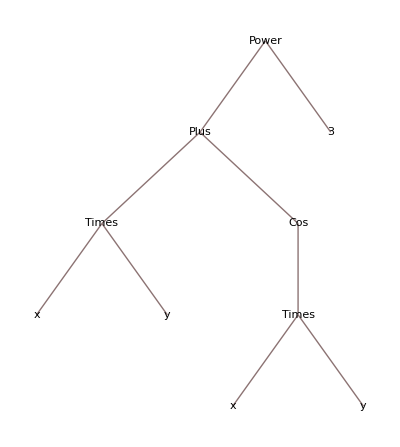

Set::write: Tag List in {{3\ ⅇ^3\ x + x\ y\ y\ Cos[ⅇ^x\ y] + ⅇ^3\ x + x\ y\ y\ (3 + y)\ Cos[ⅇ^x\ y] + 9\ ⅇ^3\ x\ Sin[ⅇ^x\ y] - ⅇ^3\ x + 2\ x\ y\ y^2\ Sin[ⅇ^x\ y], ⅇ^3\ x + x\ y\ Cos[ⅇ^x\ y] + 3\ ⅇ^3\ x + x\ y\ x\ Cos[ⅇ^x\ y] + ⅇ^3\ x + x\ y\ x\ y\ Cos[ⅇ^x\ y] - ⅇ^3\ x + 2\ x\ y\ x\ y\ Sin[ⅇ^x\ y]}, {ⅇ^3\ x + x\ y\ Cos[ⅇ^x\ y] + ⅇ^3\ x + x\ y\ x\ (3 + y)\ Cos[ⅇ^x\ y] - ⅇ^3\ x + 2\ x\ y\ x\ y\ Sin[ⅇ^x\ y], ⅇ^3\ x + x\ y\ x^2\ Cos[ⅇ^x\ y] - ⅇ^3\ x + 2\ x\ y\ x^2\ Sin[ⅇ^x\ y]}}[x_, y_, z_] is Protected.

```mathematica
pred=Table[{},{7}];
suc=Table[{},{7}];
pred[[4]]={1,2};
pred[[5]]={2,3,4};
pred[[6]]={4,5};
pred[[7]]={4,6};
suc[[1]]={4};
suc[[2]]={4};
suc[[3]]={7};
suc[[4]]={5,6};
suc[[5]]={6};
suc[[6]]={7};
f4[{x_,y_}]=x y;
f5[{x_}]=Cos[x];
f6[{x_,y_}]=x + y;
f7[{x_,y_}]=x^3;
func={f4,f5,f6,f7};
f[x_,y_,z_]=f7[{f6[{f5[{f4[{x,y}]}],f4[{x,y}]}],z}];
TreeForm[f[x,y,z]]
d = {1,1,1};
vars = {x,y,z};
numvar = Length[vars];
numnos = numvar + Length[func];
gradd[x_,y_,z_]= D[f[x,y,z],{vars,1}];
hesstest[x_,y_,z_]= D[f[x,y,z],{vars,2}];
Tensd = D[hesstest[x,y,z].d,{vars,1}];
```

```mathematica
{vdout, vadjout,wout,Tdout}=TensVec[vars,numvar,numnos, pred,suc,func,d];
vdout /. x->1 /. y->2 /. z-> 3;
```

{1,1,1,3,1-11 Sin[6],4-11 Sin[6],36}

```mathematica
{1,1,1,3,3 Derivative[{0,0,1}][f5][{2,3,2}]+Derivative[{0,1,0}][f5][{2,3,2}]+Derivative[{1,0,0}][f5][{2,3,2}],3+3 Derivative[{0,0,1}][f5][{2,3,2}]+Derivative[{0,1,0}][f5][{2,3,2}]+Derivative[{1,0,0}][f5][{2,3,2}],36}
```

{1,1,1,3,1-11 Sin[6],4-11 Sin[6],36}

2

```mathematica
EXAMPLE TEST  Simple
pred=Table[{},{6}];
suc=Table[{},{6}];
pred[[6]]={4,5};
pred[[5]]={3};
pred[[4]]={1,2};
suc[[1]]={4};
suc[[2]]={4};
suc[[3]]={5};
suc[[4]] ={6};
suc[[5]] ={6};
f4[{x_,y_}]=x *y;
f5[{x_}] = Sin[x];
f6[{x_,y_}]=x y;
func={f4,f5, f6};
fun1[x_,y_,z_] = f6[{f4[{x,y}],f5[{z}]}]
TreeForm[fun1[x,y,z]];
d = {1,1,1};
vars = {x,y,z};
numvar = Length[vars]
numnos = numvar + Length[func]
gradtest[x_,y_,z_]= D[fun1[x,y,z],{vars,1}]
hesstest[x_,y_,z_]= D[fun1[x,y,z],{vars,2}]
Tensd = D[hesstest[x,y,z].d,{vars,1}];
Tenswhole =D[hesstest[x,y,z],{vars,1}];
```

EXAMPLE Simple TEST

x y Sin[z]

3

6

{y Sin[z],x Sin[z],x y Cos[z]}

{{0,Sin[z],y Cos[z]},{Sin[z],0,x Cos[z]},{y Cos[z],x Cos[z],-x y Sin[z]}}

```mathematica
{vdout, vadjout,wout,Tdout}=TensVec[vars,numvar,numnos, pred,suc,func,d];
auxtemp = Range[1,numvar];
vdout/. x->1 /. y->2;

Print["vadjoint: ",vadjout];
Print["Wout",MatrixForm[Simplify[wout]]];
Print["Tdout",MatrixForm[Simplify[Tdout]]];

Simplify[Tdout[[auxtemp,auxtemp]]-Tensd];
```

-Graphics-

vadjoint: {y Sin[z],x Sin[z],x y Cos[z],Sin[z],x y,1}

Wout(0 | Sin[z] | 0 | 0 | 0 | 0
Sin[z] | 0 | 0 | 0 | 0 | 0
0 | 0 | -x y Sin[z] | Cos[z] | 0 | 0
0 | 0 | Cos[z] | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

Tdout(0 | 0 | 0 | 0 | 0 | 0
Cos[z] | 0 | 0 | 0 | 0 | 0
Cos[z]-y Sin[z] | Cos[z]-x Sin[z] | -x y Cos[z]-(x+y) Sin[z] | 0 | 0 | 0
0 | 0 | -Sin[z] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)